```mathematica
ClearAll["Global`*"]
```

```mathematica
toR3[{{a_,b_},{c_,d_}}]:={a,(b+c)/2, (b-c)/(2 I) }
sf[α_,l_,m_]:=Module[{s,δ},
s = {l,m}//Transpose;
δ = DiagonalMatrix[{λ-α, 1}];
Return[s.δ.Inverse[s]]
]
normInf[z_]:=Max[Abs[Re[z]],Abs[Im[z]]]
spinor[({{a_, b_}, {c_, d_}})]:={Sqrt[b], Sqrt[-c]}
```

## Catenoid

```mathematica
λ0=0;
λ1=1;
p = 1/4;
q=1;
k = ({{0, 1}, {q λ +p, 0}});
ξ = k/z;
spin = spinor[D[ξ,λ]];
c = 1/Sqrt[2]({{1, 1/μ}, {-μ, 1}})/.μ->Sqrt[p];
Φ = c.MatrixExp[k Log[z]]//Simplify;
ξ= Inverse[Φ].D[Φ,z]//Simplify;
spin = Φ.spinor[D[ξ, λ]]//Simplify;
gauss = spin/.λ->λ0//(#[[1]])/(#[[2]])&//FullSimplify;
Ψ=D[Φ,λ].Inverse[Φ]/.λ->λ0//Simplify;
f = Ψ+ConjugateTranspose[Ψ]//Simplify
x=toR3[f]//Simplify;
w = Log[μ]/(2μ)/.μ->Sqrt[p];
```

{{Conjugate[Log[z]]+Log[z],5/2-2 z-1/(2 Conjugate[z])},{5/2-1/(2 z)-2 Conjugate[z],-Conjugate[Log[z]]-Log[z]}}

```mathematica
ParametricPlot3D[x/.z->Exp[u+I v],{u,w-3,w+3},{v,-Pi,Pi},RegionFunction->((normInf[(#4+I #5)-1]>0.5)&)]
```

-Graphics3D-

## Dressed catenoid 2 planes straight

```mathematica
α = (n^2-1)/(4 q)/.n->2;
μ2 = q λ + p;
μ0 = Sqrt[μ2]/.λ->0//Simplify;
μα = Sqrt[μ2]/.λ->α//Simplify;
(*l1Val = l1->(-4+2 Log[8] (-2+4 Log[2]^2+Log[8]))/(-6+4 Log[2]^3+Log[2] (-18+Log[8]));*)
(*l1Val = l1->14/13*)
(*Clear[l1]*)
l = {14/13,1};
m = {0,1};
{z1,z2}= z/.Solve[-(μ0(z^(2μα)-1)+μα(z^(2μα)+1))l[[2]]==μ0(μ0(z^(2μα)-1)-μα(z^(2μα)+1))l[[1]],z];
g = sf[α, l, m];
g0 = g/.λ->0;
gg = Sqrt[Det[g0]]Inverse[g0].g//Simplify;
h = sf[α,Inverse[Φ].l/.λ->α, {0,1}]//Simplify;
Φ2 = gg.Φ.Inverse[h]//Simplify;
ξ2 = Inverse[Φ2].D[Φ2,z]//Simplify;
spin2 = Φ2.spinor[D[ξ2, λ]]//Simplify;
gauss2 = spin2/.λ->λ0//(#[[1]])/(#[[2]])&//FullSimplify;
Ψ=D[Φ2,λ].Inverse[Φ2]/.λ->λ0//Simplify;
f = Ψ+ConjugateTranspose[Ψ]//Simplify;
x=toR3[f]/.z->Exp[u+I v]//Re//ExpToTrig//FullSimplify[#,Element[u|v,Reals]]&;
```

```mathematica
r=0.01;
center = 1/2((1/(2Pi)Integrate[x/.u->w+1,{v,0,2Pi}])+(1/(2Pi)Integrate[x/.u->w-1,{v,0,2Pi}]))//Re;
ParametricPlot3D[x-center,{u,w-4,w+4},{v,0,2Pi},RegionFunction->Function[{x,y,z,u,v},normInf[(Exp[u+I v])-z1]>r&& normInf[(Exp[u+I v])-z2]>r && -7<x<7&&-7<y<7&&-7<z<7],MaxRecursion->0, PlotPoints->{120,60}, Mesh->All,BoxRatios->{1, 1, 1},Method->{"RotationControl"->"ArcBall"},PlotRange->Table[{-6,6},3],PerformanceGoal->"Quality", PlotStyle->Opacity[0.9],Boxed->False, Axes->True]
```

-Graphics3D-

#### fundamental piece:

```mathematica
ParametricPlot3D[x-center,{u,w,w+4},{v,0,Pi/2},RegionFunction->Function[{x,y,z,u,v},normInf[(Exp[u+I v])-z1]>r&& normInf[(Exp[u+I v])-z2]>r && -7<x<7&&-7<y<7&&-7<z<7],MaxRecursion->0, PlotPoints->{60,30}, Mesh->All,BoxRatios->{1, 1, 1},Method->{"RotationControl"->"ArcBall"},PlotRange->All,PerformanceGoal->"Quality", PlotStyle->Opacity[0.9],Boxed->False, Axes->True]
```

-Graphics3D-

## discrete plot

#### a discrete domain with a pole at {0,0}

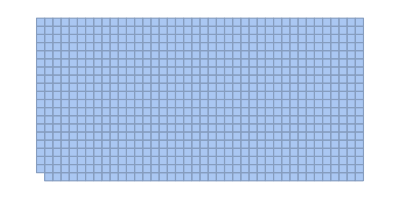

```mathematica
makeArray[j_,k_]:=Table[Table[1,k],j]
makeArrayWithPole[j_,k_]:=Join[makeArray[j-1,k],{Join[{0},Table[1,k-1]]}]
discreteRectangle = ArrayMesh[makeArrayWithPole[20,40],DataRange->{{w,w+Pi},{0,Pi/2}}]
```

```mathematica
curvatureRefinementFunction = Function[{vertices,area},area (curvature[{u,v}]/.{u->Mean[vertices][[1]],v->Mean[vertices][[2]]})>0.15];
metricRefinementFunction = Function[{vertices,area},area (metric[{u,v}]/.{u->Mean[vertices][[1]],v->Mean[vertices][[2]]})>0.25];
refinementFunction = Function[{vertices,area},metricRefinementFunction[vertices,area]||curvatureRefinementFunction[vertices,area]];
```

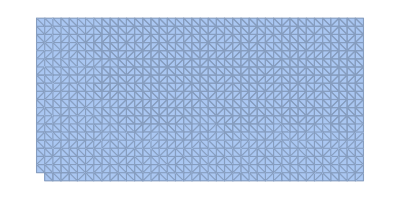

```mathematica
discreteDomain =TriangulateMesh[discreteRectangle]
```

#### Computing the surface data

```mathematica
map[{u_,v_}]= x-center;
```

```mathematica
points = MeshCoordinates[discreteDomain];
faces = MeshCells[discreteDomain,2];
pointsInSpace = map/@points;
surface=Graphics3D[{EdgeForm[],GraphicsComplex[pointsInSpace,faces]},Boxed->False,Axes->False]
```

-Graphics3D-

#### Exporting as JSONs

to make a uv map between 0 and 1:

```mathematica
max = Max[points];
min = Min[points];
lin[{u_,v_}]={(u-min)/(max-min), (v-min)/(max-min)};
```

```mathematica
facesList = faces[[All,1]];
data = {points, facesList, pointsInSpace};
Export["/home/thomas/python/objParser/input/faces.json",facesList]
Export["/home/thomas/python/objParser/input/points.json",pointsInSpace]
Export["/home/thomas/python/objParser/input/uv.json",lin/@points]
```

/home/thomas/python/objParser/input/faces.json

/home/thomas/python/objParser/input/points.json

/home/thomas/python/objParser/input/uv.json

#### Run obj-helper.py to get the obj.